## Load packages and global definitions

```mathematica
SetDirectory[NotebookDirectory[]];
Get["../Mathematica_packages/QMB.wl"]
Get["../Mathematica_packages/Chaometer.wl"]
```

```mathematica
(* Define the collective spin operators for L spins*)
Clear[Jx,Jy,Jz,L];
Jx[L_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,Pauli[1],IdentityMatrix[2]],{j,L}],{i,L}];
Jy[L_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,Pauli[2],IdentityMatrix[2]],{j,L}],{i,L}];
Jz[L_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,Pauli[3],IdentityMatrix[2]],{j,L}],{i,L}];
```

```mathematica
(* LMG Hamiltonian *)
LMGHamiltonian[α_,β_,L_]:=N[Normal[α*Jz[L]+β/L(Jx[L].Jx[L])]]
```

# Purity of Choi matrix

## Calculations

```mathematica
L=10;(* number of spins *)
α=-0.45;β=3*α;
```

Compute LMG Hamiltonian

```mathematica
{eigenvalsH,eigenvecsH}=Transpose[Sort[Transpose[Eigensystem[LMGHamiltonian[α,β,L]]]]];
```

Define three initial states for the environment: coherent state (1,1), coherent random state, product of random states

```mathematica
SeedRandom[138021+10];
ψE={coherentstate[qubit[Pi,2Pi],L-1],coherentstate[qubit[RandomReal[],RandomReal[]],L-1],RandomChainProductState[L-1]};
```

```mathematica
Superoperator[0,ψE[[2]],eigenvalsH,eigenvecsH,L]
```

{{1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.},{0.+0. ⅈ,1.+7.95738×10^-18 ⅈ,0.,0.+0. ⅈ},{0.+0. ⅈ,0.,1.-7.95738×10^-18 ⅈ,0.+0. ⅈ},{0.,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ}}

Compute the superoperator for 0<=t<=50 (Δt=0.1) for every initial environmental state in ψE:

```mathematica
{t0,tf,Δt}={0,50,0.1};
AbsoluteTiming[superoperators=Chop[Table[Superoperator[#,i,eigenvalsH,eigenvecsH,L]&/@Range[t0,tf,Δt],{i,ψE[[3;;3]]}]];]
```

{249.157,Null}

Export superoperators data

```mathematica
Export["/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/lipkin/vie_25_oct_2024_1.mx",superoperators,"MX"];
```

```mathematica
superoperators//Dimensions
```

{1,501,4,4}

```mathematica
chois=1/2*Map[Reshuffle,superoperators,{2}];
```

```mathematica
choiPurities=Chop[Map[Purity,chois,{2}]];
```

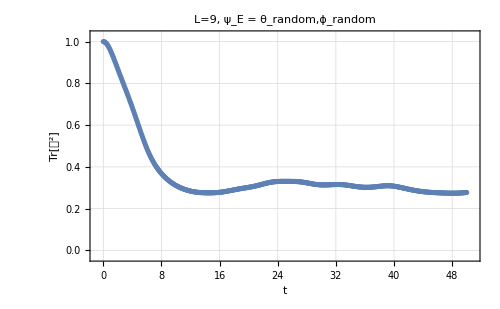

```mathematica
ListPlot[Transpose[{Range[0,50,0.1],choiPurities[[1]]}],
PlotRange->{{-0.8,50.8},{-0.03,1.03}},
Frame->True,
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->22],
GridLines->Automatic,
ImageSize->500,
PlotLabel->ToString[TraditionalForm[HoldForm[L=9]]]<>", ψ_E = θ_random,ϕ_random",
LabelStyle->Directive[Black,FontSize->17]
]
```

## Fixing L=10

```mathematica
L=10;(* number of spins *)
α=-0.45;β=3*α;
```

Compute LMG Hamiltonian

```mathematica
{eigenvalsH,eigenvecsH}=Chop[Transpose[Sort[Transpose[Eigensystem[LMGHamiltonian[α,β,L]]]]]];
```

```mathematica
eigenvecsH=Orthogonalize[eigenvecsH];
```

```mathematica
SeedRandom[138021];
ψE={coherentstate[qubit[Pi,2Pi],L-1],coherentstate[qubit[RandomReal[],RandomReal[]],L-1],RandomChainProductState[L-1]};
```

```mathematica
Chop[Superoperator[0,ψE[[2]],eigenvalsH,eigenvecsH,L]]
```

{{1.,0,0,0},{0,1.,0,0},{0,0,1.,0},{0,0,0,1.}}

```mathematica
?StateEvolution
```

```mathematica
StateEvolution[0.,KroneckerVectorProduct[{1,0},ψE[[1]]],eigenvalsH,eigenvecsH]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}